The purpose of this exercise is to learn Mathematica. We do this by solving some general biological problems.

1. Bacterial Growth
We start with Bacterial Growth. The Bacteria are inoculated in a petri dish at a density of 10/ml. We know that the following differential equation describes this situation:

ⅆx/ⅆt = C x

Where x is the bacterial density and C is a constant. And that the bacterial density doubles in twenty hours. By integrating this equation giving x as a function of time, we find the value of C.

```mathematica
Clear[x]
(* Solve for the integral that has value 10 at starting t = 0. *)
solution = DSolve[{x'[t] == C x[t], x[0] == 10}, x[t], t]

(* Assign the solution to function x. *)
x[t_] = x[t]/.solution⟦1⟧

(* What is the numerical value of C? *)
Solve[x[20] == 20, C, Reals]
N[%]

(* Assign a value to C. *)
x[t_] = x[t]/.Solve[x[20] == 20, C, Reals]
```

{{x[t]→10 ⅇ^(C t)}}

10 ⅇ^(C t)

{{C→Log[2]/20}}

{{C→0.0346574}}

{5 2^(1+t/20)}

Next, we plot the fitted Curve and solve for the times that it takes the density to increase to eight and ten times its original value.

{{0,10},{20,20}}

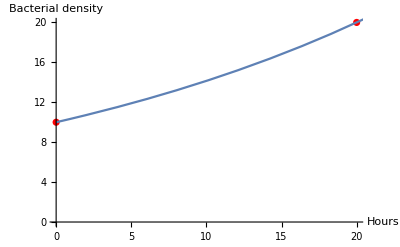

{{t→60}}

{{t→(20 (Log[2]+Log[5]))/Log[2]}}

{{t→66.4386}}

```mathematica
(* Data points *)
d = {{0,10},{20,20}}

(* Why does it not plot untill 100 hrs here? *)Show[ListPlot[d, PlotStyle->Red], Plot[x[t], {t,0,100}],AxesLabel->{Hours, Bacterial density}]

Solve[x[t] == 80, t, Reals]
Solve[x[t] == 100,t, Reals]
N[%]
```

It takes the bacteria 60 hours to increase to eight times its original value, and 66,4 hours to increase to ten times its original value.

2. Fitting linear or exponential functions to growth data
In this exercise, there is a dataset that we need to fit a function too, and we ask ourselves the question, what describes this form of growth better, an exponential or linear function? We find this out by fitting the functions, plotting them with the data, and finding the errors of both fits.

We plot a linear function of the form y=ax+b, and an exponential function of the form y=ae^bx.

ⅇ^(j x) i

-15.9278+24.9788 x

2.1846 ⅇ^(1.3218 x)

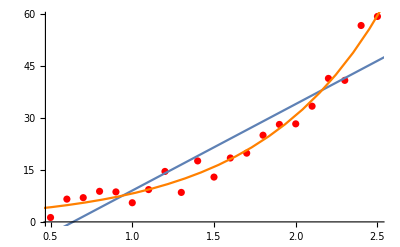

```mathematica
Clear[x]
Clear[a]
Clear[b]
Clear[i]
Clear[j]

myData={{0.5,1.27},{0.6,6.58},{0.7,7.00},{0.8,8.83},{0.9,8.66},{1.0,5.53},{1.1,9.33},{1.2,14.57},{1.3,8.51},{1.4,17.61},{1.5,12.94},{1.6,18.45},{1.7,19.85},{1.8,25.03},{1.9,28.14},{2.0,28.31},{2.1,33.41},{2.2,41.43},{2.3,40.87},{2.4,56.71},{2.5,59.32}};

efunc[x_] = i * Exp[j* x]

(*Find fit*)
linearFit = Fit[myData,{1,x},x]

(* Assign values to i and j *)
efunc[x_] = efunc[x]/.FindFit[myData,efunc[x],{i,j},x]

(*Plot fit*)
Show[ListPlot[myData, PlotStyle->Red], Plot[linearFit,{x,0,5}],Plot[efunc[x], {x,0,5}, PlotStyle->Orange]]

(*Calculate error of fit*)
```

After finding out that the best fit is with the exponential curve, we find its differential equation, with numerical values: XXXXXXXXXXXX.

3. SIR Model - Seasonal epidemics
With the SIR model we study how the probability of getting a disease varies with the seasons of the year. SIR stands for Susceptibility-Infection-Recovery and is a set of nonlinear differential equations, with periodically varying parameters. The periodically forced SIR model is:

dS/dt=μ-μ S-β(t)I S
dI/dt=β(t)I S-(γ+μ)I
dR/dt=γ I-μ R

Here S, I and R are the fractions of susceptible, infective and recovered individuals in the population. μ is the birth and death rate; β(t) is the seasonally dependent infection rate; and γ is the recovery rate. We take β(t) to be periodic; β(t)=β_0[1+sin((2π t)/T)], where T is the length of the infection season and β_0 is a constant. The reproduction number for this system is 1/T∫_0^T (β(t))/(μ+γ)dt; if the integral is greater than one, the disease will not disappear and may undergo interesting and complex phenomena of nonlinear parametric resonance . 

We want to study these phenomena, and see how S, I and R change over time with varying parameters. We made plots to analyze how the dynamics change by varying the death rate over the domain [0, 1], recovery rate [0,1], season length T [0,30], initial infection rate [0,1] and the fraction of initially infected [0, 1].

```mathematica
Remove[sus]
Remove[inf]
Remove[rec]

(* not yet seasonal - infection rate *)
beta = 0.2

(* Rate of recovery *)
gamma = 1/15

(* Fractions of initial S, I and R *)
tzero = {0.95,0.05,0.0};

(* Set of ODEs. *)
eqns = {
sus'[t] == - beta*inf[t]*rec[t], 
inf'[t] == beta *inf[t]*sus[t], 
rec'[t] == gamma * inf[t] , 
sus[0]==tzero⟦1⟧, inf[0] == tzero⟦2⟧, rec[0]== tzero⟦3⟧};

solutions = NDSolve[eqns, {sus[t],inf[t],rec[t]}, t]

sus[t_] = solutions⟦1⟧
inf[t_] = solutions⟦2⟧
rec[t_] = solutions⟦3⟧

Plot[sus[t], {t,0,50}]
```

0.2

1/15